```mathematica
LogIntegralEurope[x_]:=LogIntegral[x]-LogIntegral[2]
```

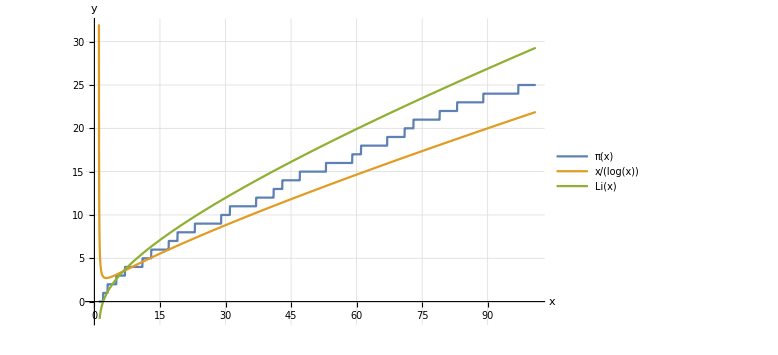

/Users/Flo/Dropbox/Schule/3. W-Seminar/jupyter/zeta/pi-prime-count-100.pdf

```mathematica
Plot[{PrimePi[x],x/Log[x], LogIntegralEurope[x]},{x,1,101}, AxesLabel->{x,y}, ImageSize->Large, PlotTheme->"Default", GridLines->Automatic, PlotRange->{-2,32}, PlotLegends->{Pi[x],x/Log[x],Li[x]}]
Export["/Users/Flo/Dropbox/Schule/3. W-Seminar/jupyter/zeta/pi-prime-count-100.pdf",%,"PDF"]
```

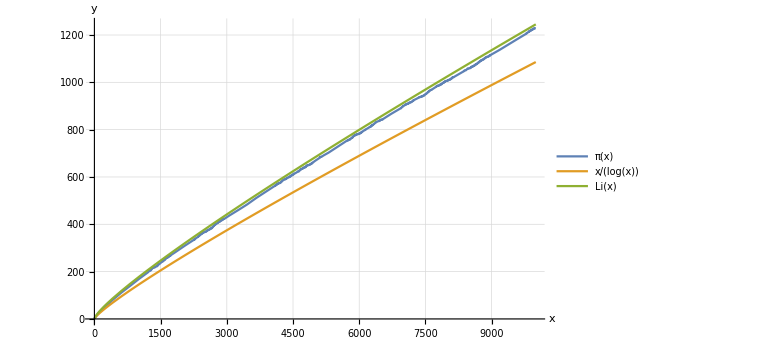

/Users/Flo/Dropbox/Schule/3. W-Seminar/jupyter/zeta/pi-prime-count-10000.pdf

```mathematica
Plot[{PrimePi[x],x/Log[x], LogIntegralEurope[x]},{x,2,10000}, AxesLabel->{x,y}, ImageSize->Large, PlotTheme->"Default", GridLines->Automatic, PlotRange->Automatic, PlotLegends->{Pi[x],x/Log[x],Li[x]}]
Export["/Users/Flo/Dropbox/Schule/3. W-Seminar/jupyter/zeta/pi-prime-count-10000.pdf",%,"PDF"]
```

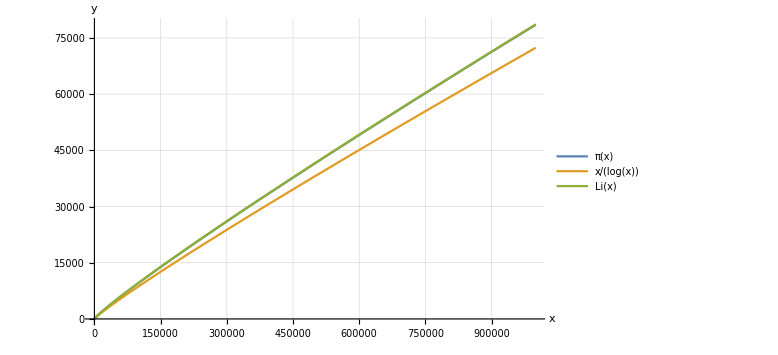

/Users/Flo/Dropbox/Schule/3. W-Seminar/jupyter/zeta/pi-prime-count-1000000.pdf

```mathematica
Plot[{PrimePi[x],x/Log[x], LogIntegralEurope[x]},{x,2,1000000}, AxesLabel->{x,y}, ImageSize->Large, PlotTheme->"Default", GridLines->Automatic, PlotRange->Automatic, PlotLegends->{Pi[x],x/Log[x],Li[x]}]
Export["/Users/Flo/Dropbox/Schule/3. W-Seminar/jupyter/zeta/pi-prime-count-1000000.pdf",%,"PDF"]
```

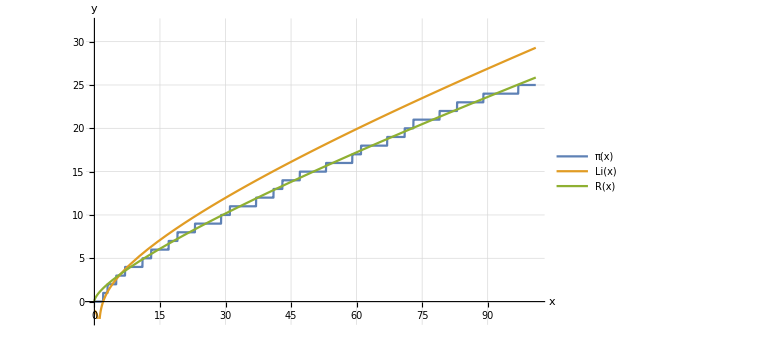

/Users/Flo/Dropbox/Schule/3. W-Seminar/jupyter/zeta/pi-prime-count-100-r.pdf

```mathematica
Plot[{PrimePi[x], LogIntegralEurope[x], RiemannR[x]},{x,0,101}, AxesLabel->{x,y}, ImageSize->Large, PlotTheme->"Default", GridLines->Automatic, PlotRange->{-2,32}, PlotLegends->{Pi[x],Li[x],R[x]}]
Export["/Users/Flo/Dropbox/Schule/3. W-Seminar/jupyter/zeta/pi-prime-count-100-r.pdf",%,"PDF"]
```